```mathematica
RGBColor[0,246,227]
```

RGBColor[0, 246, 227]

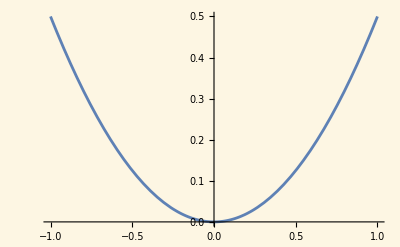

```mathematica
Plot[x^2/2,{x,-1,1}, Ticks->None,Background->RGBColor["#fdf6e3"]]
```

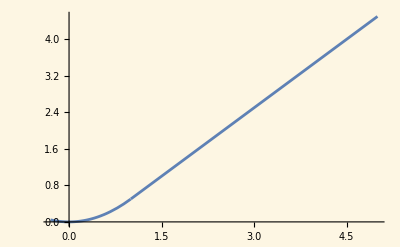

```mathematica
Plot[If[x>1,x-1/2,x^2/2],{x,-0.3,5}, Ticks->None,Background->RGBColor["#fdf6e3"]]
```

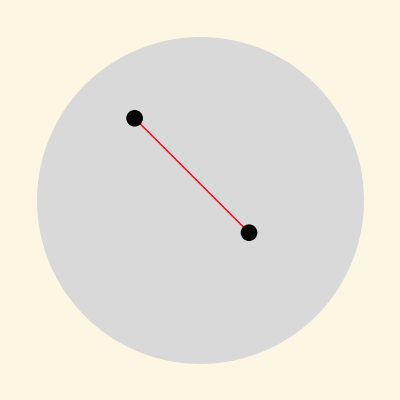

```mathematica
(*Define a convex set:a disk*)convexSet=Disk[{0,0},1];

(*Define two interior points*)
p1={0.3,-0.2};
p2={-0.4,0.5};

(*Draw the picture*)
Graphics[{LightGray,convexSet,Thick,Red,Line[{p1,p2}],Black,PointSize[0.03],Point[{p1,p2}]},Axes->False,AspectRatio->1,Background->RGBColor["#fdf6e3"]]
```

```mathematica
p1={-1,1};p2={1,1}
```

{1,1}

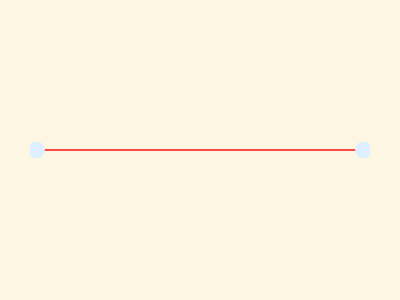

```mathematica
Graphics[{Thick,Red,Line[{p1,p2}],LightBlue,PointSize[0.03],Point[{p1,p2}]},Background->RGBColor["#fdf6e3"]]
```

```mathematica
Show[{Plot[x^2/2,{x,-1,1}, Ticks->None,Background->RGBColor["#fdf6e3"]],Graphics[{Thick,Red,Line[{p1,p2}],LightBlue,PointSize[0.03],Point[{p1,p2}]}, Ticks->None]}]
```

-Graphics-

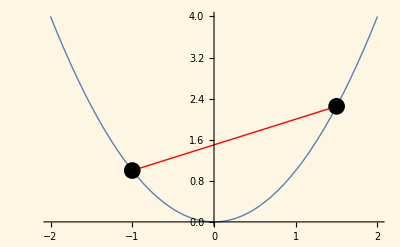

```mathematica
(*Define a convex function*)f[x_]:=x^2

(*Choose two x-values*)
x1=-1;
x2=1.5;

p1={x1,f[x1]};
p2={x2,f[x2]};

Show[{Plot[f[x],{x,-2,2},PlotStyle->Thick,Background->RGBColor["#fdf6e3"],Ticks->None],Graphics[{Red,Thick,Line[{p1,p2}],Black,PointSize[0.03],Point[{p1,p2}]}]},Axes->True]
```

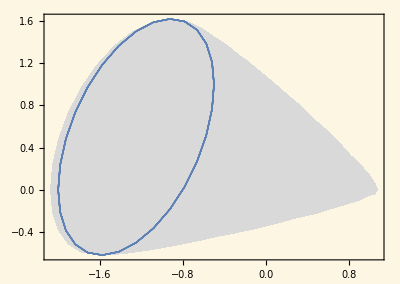

```mathematica
ParametricPlot[{z^2-0.5x^2-2*y^2-z*y,x^2+2*x*y}/.{x->Cos[theta],y->Sin[theta]*Cos[phi],z->Sin[theta]*Sin[phi]},{theta,-Pi,Pi},{phi, -Pi, Pi},Background->RGBColor["#fdf6e3"], Ticks->None,PlotStyle->{LightGray, Opacity[1]}, Axes->False]
```

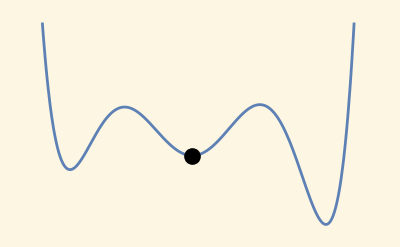

```mathematica
Plot[(x+0.9)(x-0.5)(x-0.2)(x+0.3)(x+0.6)(x-0.9),{x,-1,1},Axes->False,Background->RGBColor["#fdf6e3"],Epilog->{Black,PointSize[0.03],Point[{-0.046987410904630454,-0.015269645115496116}]}]
```

```mathematica
Expand[D[(x+0.9)(x-0.5)(x-0.2)(x+0.3)(x+0.6)(x-0.9),x]]
```

0.02916+0.603 x-0.594 x^2-4.64 x^3+1. x^4+6 x^5

```mathematica
NSolve[0.02915999999999999+0.603 x-0.5939999999999996 x^2-4.64 x^3+1.0000000000000007 x^4+6 x^5==0]
```

{{x→-0.794933},{x→-0.461274},{x→-0.0469874},{x→0.366154},{x→0.770374}}

```mathematica
(x+0.9)(x-0.5)(x-0.2)(x+0.3)(x+0.6)(x-0.9)/.{x->-0.046987410904630454}
```

-0.0152696